-Graphics-

Done, evaluating.

Plotting living boids.

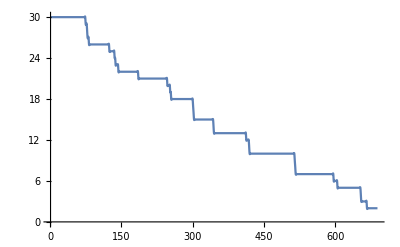

Plotting population decline.

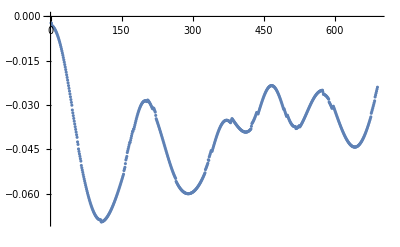

```mathematica
ClearAll["Global`*"];

(* Initial declarations*)

threeDimensional = False;(* Change to True to switch to 3D map *)

numberBoids = 30;
speedBoid = 0.05;

speedHunterSlow = 0.06;(* Speed of hunter in sight of target boid *)
speedHunterFast = 0.15;(* Speed of hunter out of sight of target boid *)

groupMembers = 5;(* Number of boids to be considered by each boid *)

(* Calculated initial conditions *)

searchCount=0;

If[threeDimensional,
boidHunter = ConstantArray[-5,3];
boidList = RandomReal[{-1,1},{numberBoids,3}];
origin = ConstantArray[0,3];,
boidHunter = ConstantArray[-5,2];
boidList = RandomReal[{-1,1},{numberBoids,2}];
origin = ConstantArray[0,2];
]

weight=N[Normalize[Exp[PadLeft[Range[groupMembers],groupMembers]]]/Total[Normalize[Exp[PadLeft[Range[groupMembers],groupMembers]]]]];(* Constant weighted array *)
(* The above line inside of N[] calculate at what range should the boids react to the hunter *)
(* Right now, it is an exponential function to simulate the "fountain movement" as best as possible *)
(* The function PadLeft is there to prevent them from reacting too early *)
(* weight={(1/55),(2/55),(3/55),(4/55),(5/55),(6/55),(7/55),(8/55),(9/55),(10/55)} *)

lastList = boidList;(* Remembers previous coordinates of boids *)
boidHunterLast = boidHunter;(* Remembers previous coordinates of hunter *)

numBoidsList={Length[boidList]};(* Keeps a record of the number of boids alive in each frame *)

If[threeDimensional,(* Random vector function *)
randomVec := RandomReal[{-1,1},3];,
randomVec := RandomReal[{-1,1},2];
]

(* Functions *)

huntList := Append[boidList,boidHunter];(* Declares a coordinate list with boids and the hunter *)

targetBoid:=Nearest[boidList->Automatic,boidHunter][[1]];(* Function selects boid to hunt *)

hunterVectorSlow:= Normalize[(* Normalised movement vector for the hunter *)
			+ hunterTarget
			-boidHunter
			+ ((boidHunter - boidHunterLast)/speedHunterSlow)*4];
hunterVectorFast:= Normalize[
			+ hunterTarget
			-boidHunter
			+ ((boidHunter - boidHunterLast)/speedHunterFast)*4];

boidVector:=Normalize[
If[EuclideanDistance[boidHunter,boidList[[i]]]<2,
((* General boid moevement *)
vecToMean*2(*Vector towards nearby boids*)
+(-boidList[[i]]
)*0.1 (*vector towards center*)
+randomVec*0.2) (*Random motion*)
+Normalize[(boidList[[i]]-boidHunter)]*(1/(EuclideanDistance[boidList[[i]],boidHunter])+0.1) (*Vector away from hunter, scaled up as hunter is closer*)
+ ((boidList[[i]] - lastList[[i]])/speedBoid)*3 (*Boid Momentum*)
,
((* General boid moevement *)
vecToMean*2(*Vector towards nearby boids*)
+(-boidList[[i]]
)*0.1 (*vector towards center*)
+randomVec*0.2) (*Random motion*)
+ ((boidList[[i]] - lastList[[i]])/speedBoid)*3 (*Boid Momentum*)
]]; (* Add more vectors here *)

(* Manage graphics plot *)

If[threeDimensional,
Graphics3D[{Dynamic[
MapThread[{#1,MapIndexed[Text[First@#2,#1]&,#2]}&,{{Black,If[EuclideanDistance[boidHunter,origin]>4,Green,If[EuclideanDistance[boidHunter,hunterTarget]>1.5,Blue,If[EuclideanDistance[boidHunter,hunterTarget]>1,Orange,Red]]]},{boidList,{boidHunter}}}]
]},
Axes->True,
PlotRange->6,SphericalRegion->True
],
Graphics[{Dynamic[
MapThread[{#1,MapIndexed[Text[First@#2,#1]&,#2]}&,{{Black,If[EuclideanDistance[boidHunter,origin]>4,Green,If[EuclideanDistance[boidHunter,hunterTarget]>1.5,Blue,If[EuclideanDistance[boidHunter,hunterTarget]>1,Orange,Red]]]},{boidList,{boidHunter}}}]
]},
Axes-> True,
PlotRange -> 6
]]

(* Stepped Calculations *)

For[j=1,j<20000,j++,If[Length[boidList]>1,
numBoidsList = Append[numBoidsList,Length[boidList]];(* Keep record of boids alive *)

(* Boid logic *)
For[i=1, i <=Length[boidList],i++,(* For Each Boid *)

(* Creates a mean point for centering the boid within the cluster *)
If[Length[boidList]>groupMembers,

meanPoint=Mean[WeightedData[NearestTo[boidList[[i]],groupMembers][boidList],weight]];,

(* Right now, it is an exponential function to simulate the "fountain movement" as best as possible, it is a constant vector so is calculated at the top as "weight". *)
meanPoint=Mean[WeightedData[NearestTo[boidList[[i]],Length[boidList]][boidList],
N[Normalize[Exp[PadLeft[Range[Length[boidList]],Length[boidList]]]]/Total[Normalize[Exp[PadLeft[Range[Length[boidList]],Length[boidList]]]]]]]]
];(**HERE**)

vecToMean = Normalize[meanPoint - boidList[[i]]]*(EuclideanDistance[meanPoint, boidList[[i]]]-0.7);

lastList = boidList;
boidList[[i]] += boidVector *speedBoid ;
];

(* This is for hunting the birds directly *)
boidHunterTemp = boidHunter;
hunterTarget = boidList[[targetBoid]]+(boidList[[targetBoid]]-lastList[[targetBoid]])*3;

If[EuclideanDistance[boidHunter,hunterTarget]>1.5,
If[EuclideanDistance[boidHunter,origin]>4,

hunterVector=Normalize[origin-boidHunter];
boidHunterTemp+=hunterVector*speedHunterFast;,

If[searchCount>10,
searchCount=0;
hunterVector=Normalize[randomVec];
boidHunterTemp+=hunterVector*speedHunterFast;,
searchCount+=1;
boidHunterTemp+=hunterVector*speedHunterFast;
]
],
searchCount=0;
If[EuclideanDistance[boidHunter,boidList[[targetBoid]]]>1,

boidHunterTemp +=hunterVectorSlow*speedHunterSlow;,

boidHunterTemp+=hunterVectorFast*speedHunterFast;
]
];


huntListCheck = huntList;
huntListCheck[[Length[huntListCheck]]] =boidHunterTemp;
boidHunterLast = boidHunter;

If[Length[huntListCheck] > 2, 
boidHunter = boidHunterTemp;
];

(*This is the eating mechanism*)
If[RankedMin[DistanceMatrix[huntList][[Length[huntList]]],2] <=0.3,
boidList = Delete[boidList,Flatten[Position[
DistanceMatrix[huntList][[Length[huntList]]],
RankedMin[DistanceMatrix[huntList][[Length[huntList]]],2]]]
[[1]]];
];

(*This is for plotting the boids and hunter*)
huntList = Append[boidList,boidHunter];

Pause[0.1];
];
];

Dynamic[Print[searchCount]];

Print["Done, evaluating."] 
a=Interpolation[numBoidsList,Method->"Spline"];
b=numberBoids-numBoidsList;
c=PadLeft[b,Length[b]+1]-PadRight[b,Length[b]+1,b[[Length[b]]]];

Print["Plotting living boids."] 
Plot[Evaluate[a[x]],{x,1,Length[numBoidsList]}]
Print["Plotting population decline."];
ListPlot[LowpassFilter[c,0.02]]
```